```mathematica
fe={6.171630936901517,31.36985492609913,10.919943958052961,0.22167710854021827,0.00023703190475858523,15.777434305648473,23.427215499458054,1.8587628689559905,0.003794028126576288,1.1439526379751184*^-7,0.7404161214996868,0.15980255907048396,0.0010837705733174473,1.0533169885174524*^-7,1.1988352159262564*^-13,0.00019502388666284122,1.4153487361645872*^-6,4.1166993979963155*^-10,5.3784696442452965*^-14,1.4362679769641991*^-15,2.785146379903139*^-10,1.0235460100281231*^-14,5.7222851979003*^-15,1.2908974684924988*^-15,3.666938476308014*^-17,2.225850290993502,73.06035547346809,147.02163346547295,22.57754081165199,0.17377517685324992,96.10218936109239,984.0057634669251,734.9365959191325,33.5571584413475,0.052139542816483926,104.94465696440353,376.24944513929427,79.18409395899597,0.5350935953558826,0.00005994494493351816,2.2460883341803566,1.3561445526575295,0.029463665151304837,0.000010588521730180234,4.430870818667075*^-11,0.00020623767979208464,7.4928175813552725*^-6,7.968727522526895*^-9,9.963009714754087*^-14,0.,0.0009012893381889533,0.9239781587365345,19.815275354777174,18.88885248744315,1.0185085027292216,5.953680352985084,470.15353029549357,1721.1876174293968,474.3874757485665,8.371731812020716,106.46483632013411,2130.82563108029,3097.7535561293535,336.2842074740427,1.5925549371983674,42.315768796805735,315.1655112456833,152.52828342854076,3.0799792066544507,0.001225425606953206,0.34212598403602656,0.509503349175655,0.03234063783385977,0.00004125249767261094,6.625368800776142*^-10,2.1108152646516083*^-11,2.067587039384483*^-6,0.002411477306185062,0.05066319165341575,0.040510034430689824,0.0001628043736542257,0.5849297357595654,36.067131018094116,77.64583797720232,8.832467465430291,0.7089023176891248,162.97323296353542,1325.4241547862916,704.8933914679592,25.209848619579063,7.143493939244727,329.4674218834638,883.309942053017,183.63915598963337,2.1747361183514995,1.1522969089466262,15.363078456154955,14.508577999163249,0.7560773818453407,0.0009959619760927794,7.286319687839942*^-16,7.870792136248886*^-15,2.0952848284245123*^-11,3.054019895039993*^-8,1.3518427007583787*^-6,2.0925193045424018*^-13,7.588923369226184*^-8,0.00032278235572420354,0.020844960755043457,0.043711022164942326,1.1475787996553808*^-6,0.015147408625147579,2.981421295116724,16.163954965341617,4.448985078523188,0.003525465775459859,2.67950325088714,58.600914887975314,70.26738361642526,5.415850460957937,0.026076579443232956,3.2040262567534463,17.646173925000724,6.801566516390516,0.22227071476821336}
```

## parámetros

```mathematica
mediay=50.;mediaz=50;
sigmay=10.; sigmaz=10.;
fy[ y_]:=PDF[NormalDistribution[mediay,sigmay],y]
fz[ z_]:=PDF[NormalDistribution[mediaz,sigmaz],z]
fyz[y_,z_]=PDF[MultinormalDistribution[{mediay,mediaz},{{sigmay^2, 0},{0,sigmaz^2}}],{y,z}]
```

0.00159155 ⅇ^(1/2 (-(0.+0.01 (-50.+y)) (-50.+y)-(0.+0.01 (-50+z)) (-50+z)))

```mathematica
Plot3D[fyz[y,z], {y, 20,80}, {z,20,80}]
```

-Graphics3D-

```mathematica
a=0.5; b=0.7711; c=-10.35534; sigmax=5.;
fx[x_, y_, z_]:=PDF[NormalDistribution[a z + b y+ c,sigmax],x]
```

```mathematica
y0=1. ; z0=2.;NIntegrate[fx[x,y0,z0], {x, 1,2.}]
```

0.0104922

```mathematica
NIntegrate[(fyz[y,z]*Integrate[fx[x, y, z],{x, 0., 1.}] ), {y, 0,1.},{ z, 0, 1} ]
```

3.77685×10^-16

```mathematica
NIntegrate[(fyz[y,z]*Integrate[fx[x, y, z],{x,-Infinity, Infinity}] ), {y,-Infinity,Infinity},{ z, -Infinity,Infinity} ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.999998

## generacion de muestras

### los datos y sus histogramas automáticos

#### n=15625

```mathematica
(5*5*5)^2
```

15625

```mathematica
SeedRandom[5613];
n = 15625; numclases=Sqrt[1. n]
ymuestra = Table[RandomVariate[NormalDistribution[mediay, sigmay]], {n}];
zmuestra = Table[RandomVariate[NormalDistribution[mediaz, sigmaz]], {n}];
xmuestra = Table[RandomVariate[NormalDistribution[a zmuestra[[i]] + b ymuestra[[i]] + c, sigmax]], {i, n}];
datosxyz=Transpose[{xmuestra, ymuestra, zmuestra}] ;
```

125.

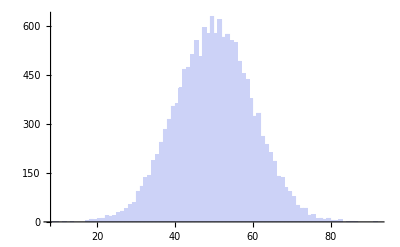

-Graphics-

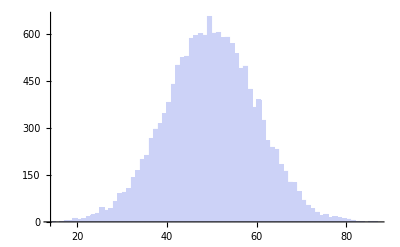

```mathematica
Histogram[zmuestra]
```

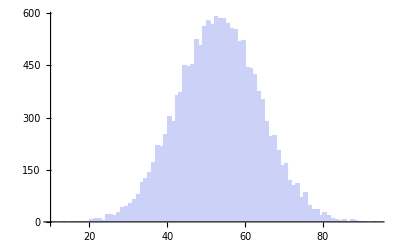

```mathematica
Histogram[xmuestra]
```

### clases

14.1175

92.254

15.6273

{14.1175,29.7448,45.3721,60.9994,76.6267,92.254}

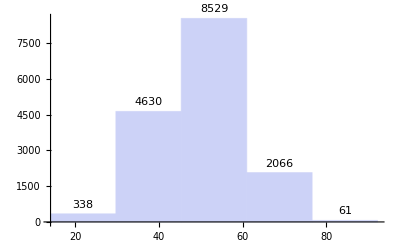

```mathematica
ymin=Min[ymuestra]
ymax=Max[ymuestra]
yincrement=(-ymin+ymax)/5
yy=Table[ymin+i*yincrement, {i, 0,5}](* la variable G *)
Histogram[ymuestra, {ymin, ymax, yincrement}, "Count",LabelingFunction->Above,PlotRange->All]
```

14.9601

92.254

15.4588

{14.9601,30.4189,45.8777,61.3364,76.7952,92.254}

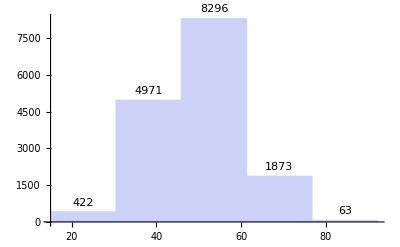

```mathematica
zmin=Min[zmuestra]
zmax=Max[ymuestra]
zincrement=(-zmin+zmax)/5
zz=Table[zmin+i*zincrement, {i, 0,5}](* la variable E *)
Histogram[zmuestra, {zmin,zmax, zincrement}, "Count",LabelingFunction->Above,PlotRange->All]
```

10.1267

93.4585

16.6664

{10.1267,26.7931,43.4594,60.1258,76.7921,93.4585}

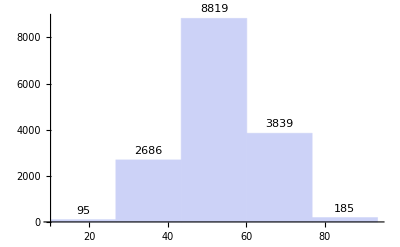

```mathematica
xmin=Min[xmuestra]
xmax=Max[xmuestra]
xincrement=(-xmin+xmax)/5
xx=Table[xmin+i*xincrement, {i, 0,5}](* la variable V *)
Histogram[xmuestra, {xmin, xmax, xincrement}, "Count",LabelingFunction->Above,PlotRange->All]
```

### conteo

```mathematica
observados=BinCounts[datosxyz, {xmin, xmax, xincrement}, {ymin, ymax, yincrement}, {zmin,zmax,zincrement}]
```

{{{3,38,15,0,0},{20,16,1,0,0},{2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{1,74,155,15,1},{105,992,748,27,0},{115,382,69,0,0},{1,1,0,0,0},{0,0,0,0,0}},{{0,0,21,14,1},{2,495,1652,441,10},{128,2157,3075,311,4},{38,291,177,2,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,38,72,11},{0,168,1356,716,26},{7,335,888,182,2},{0,18,18,2,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,3,15,2},{0,2,64,69,6},{0,2,15,6,0}}}

```mathematica
Plus@@Flatten[observados]
```

15623

## Calculo analítica

### clases extendidas

```mathematica
xx1=xx; xx1[[1]]=-Infinity; xx1[[-1]]=Infinity; 
yy1=yy; yy1[[1]]=-Infinity;yy1[[-1]]=Infinity;
zz1=zz; zz1[[1]]=-Infinity; zz1[[-1]]=Infinity;
```

```mathematica
xx1
```

{-∞,26.7931,43.4594,60.1258,76.7921,∞}

```mathematica
yy1
```

{-∞,29.7448,45.3721,60.9994,76.6267,∞}

```mathematica
zz1
```

{-∞,30.4189,45.8777,61.3364,76.7952,∞}

```mathematica
xx1=xx; xx1[[1]]=-Infinity; xx1[[-1]]=Infinity;
yy1=yy; yy1[[1]]=-Infinity;yy1[[-1]]=Infinity;
zz1=zz; zz1[[1]]=-Infinity; zz1[[-1]]=Infinity;
```

```mathematica
valores= 15625*Table[NIntegrate[(fyz[y,z]*Integrate[fx[x, y, z],{x, xx1[[i]], xx1[[i+1]]}] ), {y,yy1[[j]],yy1[[j+1]]},{ z, zz1[[k]],zz1[[k+1]]} ], {i,5}, {j,5}, {k,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.67255×10^-18 and 4.40123×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63469×10^-14 and 1.76157×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.44222×10^-18 and 3.98844×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{{6.17163,31.3699,10.9199,0.221677,0.000237032},{15.7774,23.4272,1.85876,0.00379403,1.14395×10^-7},{0.740416,0.159803,0.00108377,1.05332×10^-7,1.19884×10^-13},{0.000195024,1.41535×10^-6,4.1167×10^-10,5.37847×10^-14,1.43627×10^-15},{2.78515×10^-10,1.02355×10^-14,5.72229×10^-15,1.2909×10^-15,3.66694×10^-17}},{{2.22585,73.0604,147.022,22.5775,0.173775},{96.1022,984.006,734.937,33.5572,0.0521395},{104.945,376.249,79.1841,0.535094,0.0000599449},{2.24609,1.35614,0.0294637,0.0000105885,4.43087×10^-11},{0.000206238,7.49282×10^-6,7.96873×10^-9,9.96301×10^-14,0.}},{{0.000901289,0.923978,19.8153,18.8889,1.01851},{5.95368,470.154,1721.19,474.387,8.37173},{106.465,2130.83,3097.75,336.284,1.59255},{42.3158,315.166,152.528,3.07998,0.00122543},{0.342126,0.509503,0.0323406,0.0000412525,6.62537×10^-10}},{{2.11082×10^-11,2.06759×10^-6,0.00241148,0.0506632,0.04051},{0.000162804,0.58493,36.0671,77.6458,8.83247},{0.708902,162.973,1325.42,704.893,25.2098},{7.14349,329.467,883.31,183.639,2.17474},{1.1523,15.3631,14.5086,0.756077,0.000995962}},{{7.28632×10^-16,7.87079×10^-15,2.09528×10^-11,3.05402×10^-8,1.35184×10^-6},{2.09252×10^-13,7.58892×10^-8,0.000322782,0.020845,0.043711},{1.14758×10^-6,0.0151474,2.98142,16.164,4.44899},{0.00352547,2.6795,58.6009,70.2674,5.41585},{0.0260766,3.20403,17.6462,6.80157,0.222271}}}

```mathematica
Plus@@(Flatten[valores])
```

15625.

### Comparación (Chi-cuadrado): funciona. Los datos generados son igual a la distribución analítica

```mathematica
FO=Flatten[observados]
```

{3,38,15,0,0,20,16,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,74,155,15,1,105,992,748,27,0,115,382,69,0,0,1,1,0,0,0,0,0,0,0,0,0,0,21,14,1,2,495,1652,441,10,128,2157,3075,311,4,38,291,177,2,0,0,0,0,0,0,0,0,0,0,0,0,0,38,72,11,0,168,1356,716,26,7,335,888,182,2,0,18,18,2,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,2,0,2,64,69,6,0,2,15,6,0}

```mathematica
Length[FO]
```

125

```mathematica
FE=Flatten[valores]
```

{6.17163,31.3699,10.9199,0.221677,0.000237032,15.7774,23.4272,1.85876,0.00379403,1.14395×10^-7,0.740416,0.159803,0.00108377,1.05332×10^-7,1.19884×10^-13,0.000195024,1.41535×10^-6,4.1167×10^-10,5.37847×10^-14,1.43627×10^-15,2.78515×10^-10,1.02355×10^-14,5.72229×10^-15,1.2909×10^-15,3.66694×10^-17,2.22585,73.0604,147.022,22.5775,0.173775,96.1022,984.006,734.937,33.5572,0.0521395,104.945,376.249,79.1841,0.535094,0.0000599449,2.24609,1.35614,0.0294637,0.0000105885,4.43087×10^-11,0.000206238,7.49282×10^-6,7.96873×10^-9,9.96301×10^-14,0.,0.000901289,0.923978,19.8153,18.8889,1.01851,5.95368,470.154,1721.19,474.387,8.37173,106.465,2130.83,3097.75,336.284,1.59255,42.3158,315.166,152.528,3.07998,0.00122543,0.342126,0.509503,0.0323406,0.0000412525,6.62537×10^-10,2.11082×10^-11,2.06759×10^-6,0.00241148,0.0506632,0.04051,0.000162804,0.58493,36.0671,77.6458,8.83247,0.708902,162.973,1325.42,704.893,25.2098,7.14349,329.467,883.31,183.639,2.17474,1.1523,15.3631,14.5086,0.756077,0.000995962,7.28632×10^-16,7.87079×10^-15,2.09528×10^-11,3.05402×10^-8,1.35184×10^-6,2.09252×10^-13,7.58892×10^-8,0.000322782,0.020845,0.043711,1.14758×10^-6,0.0151474,2.98142,16.164,4.44899,0.00352547,2.6795,58.6009,70.2674,5.41585,0.0260766,3.20403,17.6462,6.80157,0.222271}

```mathematica
ffe=Round[100 FE]/100.
```

{6.17,31.37,10.92,0.22,0.,15.78,23.43,1.86,0.,0.,0.74,0.16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.23,73.06,147.02,22.58,0.17,96.1,984.01,734.94,33.56,0.05,104.94,376.25,79.18,0.54,0.,2.25,1.36,0.03,0.,0.,0.,0.,0.,0.,0.,0.,0.92,19.82,18.89,1.02,5.95,470.15,1721.19,474.39,8.37,106.46,2130.83,3097.75,336.28,1.59,42.32,315.17,152.53,3.08,0.,0.34,0.51,0.03,0.,0.,0.,0.,0.,0.05,0.04,0.,0.58,36.07,77.65,8.83,0.71,162.97,1325.42,704.89,25.21,7.14,329.47,883.31,183.64,2.17,1.15,15.36,14.51,0.76,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.02,0.04,0.,0.02,2.98,16.16,4.45,0.,2.68,58.6,70.27,5.42,0.03,3.2,17.65,6.8,0.22}

#### limpiar los caso de división por 0; FE=FO, si y solo si FE=0.

```mathematica
Position[ffe-FO,0.]==Position[ffe, 0.]
```

True

```mathematica
Length[ffe1]
```

82

```mathematica
ffe1=Delete[ffe, Position[ffe, 0.]]
```

{6.17,31.37,10.92,0.22,15.78,23.43,1.86,0.74,0.16,2.23,73.06,147.02,22.58,0.17,96.1,984.01,734.94,33.56,0.05,104.94,376.25,79.18,0.54,2.25,1.36,0.03,0.92,19.82,18.89,1.02,5.95,470.15,1721.19,474.39,8.37,106.46,2130.83,3097.75,336.28,1.59,42.32,315.17,152.53,3.08,0.34,0.51,0.03,0.05,0.04,0.58,36.07,77.65,8.83,0.71,162.97,1325.42,704.89,25.21,7.14,329.47,883.31,183.64,2.17,1.15,15.36,14.51,0.76,0.02,0.04,0.02,2.98,16.16,4.45,2.68,58.6,70.27,5.42,0.03,3.2,17.65,6.8,0.22}

```mathematica
dif=Delete[ffe-FO, Position[ffe-FO, 0.]]
```

{3.17,-6.63,-4.08,0.22,-4.22,7.43,0.86,-1.26,0.16,1.23,-0.94,-7.98,7.58,-0.83,-8.9,-7.99,-13.06,6.56,0.05,-10.06,-5.75,10.18,0.54,1.25,0.36,0.03,0.92,-1.18,4.89,0.02,3.95,-24.85,69.19,33.39,-1.63,-21.54,-26.17,22.75,25.28,-2.41,4.32,24.17,-24.47,1.08,0.34,0.51,0.03,0.05,0.04,0.58,-1.93,5.65,-2.17,0.71,-5.03,-30.58,-11.11,-0.79,0.14,-5.53,-4.69,1.64,0.17,1.15,-2.64,-3.49,-1.24,0.02,0.04,0.02,-0.02,1.16,2.45,0.68,-5.4,1.27,-0.58,0.03,1.2,2.65,0.8,0.22}

```mathematica
Length[dif]
```

82

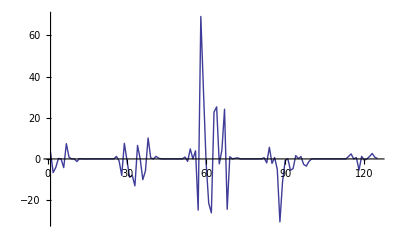

```mathematica
ListLinePlot[FE-FO, PlotRange->All]
```

```mathematica
chiCuadrado=Plus@@((dif)^2/ffe1)
```

65.9396

```mathematica
NSolve[CDF[ChiSquareDistribution[124]][x]==0.95,x]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→150.989}}